Lista de Valores de lucros total para cada margem de lucro percentual:

```mathematica
ListaLucroTotal = {265229.08999999997,572115.2999999999,825151.3,1048144.6000000001,1314299.8000000003,1444296.9000000001,1288803.0,1675737.7999999998,1704671.8000000003,1742594.6,2002088.2,1539299.2999999996,1503936.5,1680540.5,1438948.5999999999,1599596.5,1649879.0,1696750.1,1936889.5999999999,1437794.0999999999,1503360.0,1194288.2999999998,1259870.8,1238898.9000000001,1371181.0,1177971.1,1610306.1,1003514.8000000002,730176.8999999999,1095933.8};
ListaLucroTotal = Transpose[{Table[x,{x,10,300,10}],ListaLucroTotal}];
```

Ajuste dos pontos acima para uma distribuição log - normal

(A ⅇ^(-(-μ+Log[x])^2/(2 σ^2)))/(√(2 π) x σ)

{A→14570.7,μ→5.94613,σ→1.80356}

Function[{x},(3222.99 ⅇ^(-0.153712 (-5.94613+Log[x])^2))/x]

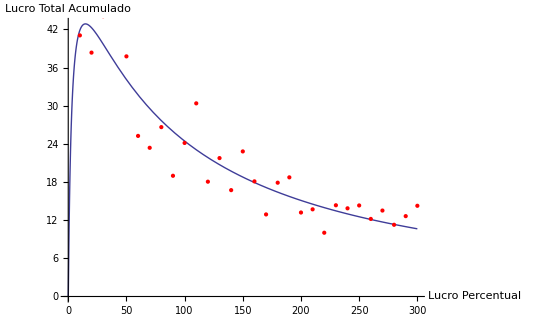

```mathematica
model = A* PDF[LogNormalDistribution[μ,σ],x] (*Densidade de Probabilidade log-normal*)
fit=FindFit[list,model,{A,μ, σ},x]
modelf=Function[{x},Evaluate[model/.fit]]
Plot[modelf[x],{x,0,300},Epilog->{PointSize[Medium],Red,Map[Point,list]},PlotRange->All,AxesLabel -> {"Lucro Percentual","Lucro Total Acumulado"}]
```